```mathematica
Remove["Global`*"];
```

Run this first to set the correct working directory

```mathematica
SetDirectory[NotebookDirectory[]]
```

# FIG 6. Available work

Compile ‘avaliablework.c’

```mathematica
Run["START /B  gcc c\\functions.c c\\avaliablework.c -o c\\avaliablework"]
```

0

Create a function that runs ‘avaliablework.exe’ for a set of inputs and sends the output to an appropriately named .dat file

```mathematica
avaliablework[asteps_,ksteps_,maxn_]:=Run["START /B c\\avaliablework "<>ToString[asteps]<>" "<>ToString[ksteps]<>" "<>ToString[maxn]<>" > data\\avaliablework-asteps"<>ToString[asteps]<>"-ksteps"<>ToString[ksteps]<>"-maxn"<>ToString[maxn]<>".dat"]
```

```mathematica
avaliablework[101,101,20]
```

0

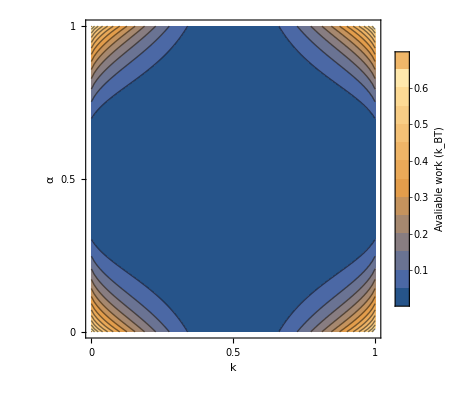

```mathematica
availableworkplot=ListContourPlot[
Import["data\\avaliablework-asteps101-ksteps101-maxn20.dat"]⟦All,{2,1,3}⟧,
FrameLabel->{"k","α"},
RotateLabel->False,
PlotRange->{{0,1},{0,1},{0,0.7}},
FrameTicks->{{0,0.5,1},{0,0.5,1}},
PlotLegends->BarLegend[
Automatic,
Ticks->Transpose[{#⟦1⟧,#⟦2⟧}&[{{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7},{"",0.1,"",0.2,"",0.3,"",0.4,"",0.5,"",0.6,"",0.7}}]],
LegendLabel->"Avaliable work\n(k_BT)"
],
Contours->{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7}
]
```

```mathematica
Export["availableworkplot.pdf",availableworkplot]
```

availableworkplot.pdf

# FIG 7. Markov and binary batch machines

## (a)

We have a simple equation for the work extracted by the Markov machine so we create a function to calculate it in pure Mathematica code.

```mathematica
markovwork[a_,k_]:=Log[2]+((1-k)(a^2+(1-a)^2)+2k a(1-a))Log[(1-k)(a^2+(1-a)^2)+2k a(1-a)]+(k(a^2+(1-a)^2)+2(1-k)a(1-a))Log[k(a^2+(1-a)^2)+2(1-k)a(1-a)]
```

Create a function that takes in a data file that contains the available work for various values of k and α and outputs a file containing the Markov efficiency at the same points.

```mathematica
markovefficiency[avaliableworkdatafilename_]:=
Export[
StringReplace[avaliableworkdatafilename,"avaliablework"->"markovefficiency"],
{#⟦1⟧,#⟦2⟧,If[#⟦3⟧==0,1,markovwork[#⟦1⟧,#⟦2⟧]/#⟦3⟧]}&/@Import[avaliableworkdatafilename]
]
```

First calculate the available work

```mathematica
avaliablework[51,51,20]
```

then calculate the Markov efficiency.

```mathematica
markovefficiency["data\\avaliablework-asteps51-ksteps51-maxn20.dat"]
```

data\markovefficiency-asteps51-ksteps51-maxn20.dat

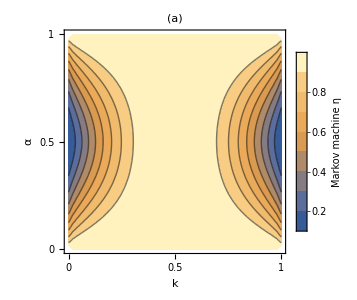

```mathematica
markovefficiencyplot=ListContourPlot[
Import["data\\markovefficiency-asteps51-ksteps51-maxn20.dat"]⟦All,{2,1,3}⟧,
FrameLabel->{"k","α"},
PlotLabel->"(a)",
PlotRange->{{0,1},{0,1}},
RotateLabel->False,
FrameTicks->{{0,0.5,1},{0,0.5,1}},
PlotLegends->BarLegend[
Automatic,
Ticks->Transpose[{#⟦1⟧,#⟦2⟧}&[{{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1},{0,"",0.2,"",0.4,"",0.6,"",0.8,"",1}}]],
LegendLabel->"Markov\nmachine η"
],
Contours->{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},
ImageSize->300
]
```

## (b)

Compile ‘simulatebatchefficiency.c’

```mathematica
Run["START /B gcc c\\functions.c c\\simulatebatchefficiency.c -o c\\simulatebatchefficiency"]
```

0

Create a function that runs ‘simulatebatchefficiency.exe’ for a set of inputs and sends the output to an appropriately named .dat file

```mathematica
simulatebatchefficiency[asteps_,ksteps_,maxn_,length_,entropyn_]:=Run["START /B c\\simulatebatchefficiency "<>ToString[asteps]<>" "<>ToString[ksteps]<>" "<>ToString[maxn]<>" "<>ToString[length]<>" "<>ToString[entropyn]<>" > data\\simulatebatchefficiency-asteps"<>ToString[asteps]<>"-ksteps"<>ToString[ksteps]<>"-maxn"<>ToString[maxn]<>"-length"<>ToString[length]<>"-entropyn"<>ToString[entropyn]<>".dat"]
```

```mathematica
simulatebatchefficiency[21,21,25,10000000,20]
```

0

For k>0.08 the binary batch efficiency is equal to the Markov efficiency so the previously calculated Markov efficiency is used.

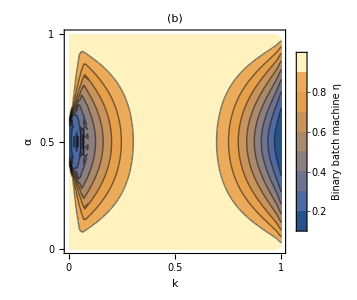

```mathematica
batchefficiencyplot=ListContourPlot[
Import["data\\simulatebatchefficiency-asteps21-ksteps21-maxn25-length10000000-entropyn20.dat"]⟦All,{2,1,3}⟧~Join~Select[Import["data\\markovefficiency-asteps51-ksteps51-maxn20.dat"]⟦All,{2,1,3}⟧,
#⟦1⟧>0.08&
],
FrameLabel->{"k","α"},
PlotLabel->"(b)",
PlotRange->{{0,1},{0,1}},
RotateLabel->False,
FrameTicks->{{0,0.5,1},{0,0.5,1}},
PlotLegends->BarLegend[
Automatic,
Ticks->Transpose[{#⟦1⟧,#⟦2⟧}&[{{0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1},{0.2,"",0.4,"",0.6,"",0.8,"",1}}]],
LegendLabel->"Binary batch\nmachine η"
],
Contours->{0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},
ImageSize->300
]
```

## (c)

Compile ‘simulatebatch.c’

```mathematica
Run["START /B gcc c\\functions.c c\\simulatebatch.c -o c\\simulatebatch"]
```

0

Create a function that runs ‘simulatebatch.exe’ for a set of inputs and sends the output to an appropriately named .dat file

```mathematica
simulatebatch[asteps_,ksteps_,maxn_,length_]:=Run["START /B c\\simulatebatch "<>ToString[asteps]<>" "<>ToString[ksteps]<>" "<>ToString[maxn]<>" "<>ToString[length]<>" > data\\simulatebatch-asteps"<>ToString[asteps]<>"-ksteps"<>ToString[ksteps]<>"-maxn"<>ToString[maxn]<>"-length"<>ToString[length]<>".dat"]
```

```mathematica
simulatebatch[21,21,25,10000000]
```

```mathematica
simulatebatch[5,5,10,1000]
```

0

Create a function that takes in a data file that contains the binary batch machine work for various values of k and α and outputs a file containing the ratio of the binary batch machine work to the Markov machine work at the same points.

```mathematica
machineratio[batchworkdatafilename_]:=
Export[
StringReplace[batchworkdatafilename,"simulatebatch"->"machineratio"],
{#⟦1⟧,#⟦2⟧,#⟦3⟧/markovwork[#⟦1⟧,#⟦2⟧]}&/@Import[batchworkdatafilename]
]
```

```mathematica
machineratio["data\\simulatebatch-asteps21-ksteps21-maxn25-length10000000.dat"]
```

data\machineratio-asteps21-ksteps21-maxn25-length10000000.dat

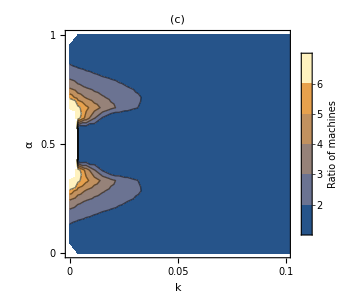

```mathematica
machineratioplot=ListContourPlot[
Import["data\\machineratio-asteps21-ksteps21-maxn25-length10000000.dat"]⟦All,{2,1,3}⟧~Join~Flatten[Table[{k,a,1},{k,0.1,1,0.1},{a,0,1,0.1}],1],
FrameLabel->{"k","α"},
PlotLabel->"(c)",
PlotRange->{{0,0.1},{0,1},{0,10}},
RotateLabel->False,
FrameTicks->{{0,0.05,0.1},{0,0.5,1}},
PlotLegends->BarLegend[
Automatic,
Ticks->{1,2,3,4,5,6},
LegendLabel->"Ratio of\nmachines"
],
Contours->{2,3,4,5,6},
ImageSize->305
]
```

## (d)

Compile ‘simulatebatchworkoptimumcontour.c’

```mathematica
Run["START /B gcc c\\functions.c c\\simulatebatchworkoptimumcontour.c -o c\\simulatebatchworkoptimumcontour"]
```

0

Create a function that runs ‘simulatebatchworkoptimumcontour.exe’ for a set of inputs and sends the output to an appropriately named .dat file

```mathematica
binarybatchoptimumn[asteps_,ksteps_,maxn_,length_]:=Run["START /B c\\simulatebatchworkoptimumcontour "<>ToString[asteps]<>" "<>ToString[ksteps]<>" "<>ToString[maxn]<>" "<>ToString[length]<>" > data\\simulatebatchworkoptimumcontour-asteps"<>ToString[asteps]<>"-ksteps"<>ToString[ksteps]<>"-maxn"<>ToString[maxn]<>"-length"<>ToString[length]<>".dat"]
```

```mathematica
binarybatchoptimumn[5,5,10,1000]
```

0

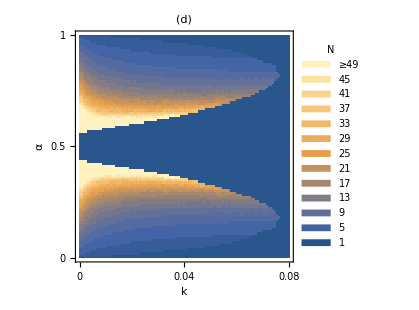

```mathematica
batchnplot=ListContourPlot[
Import["data\\simulatebatchworkoptimumcontour-asteps100-ksteps100-maxn50-length10000000.dat"]⟦All,{2,1,3}⟧,
InterpolationOrder->0,
Contours->Range[49],
PlotRange->{{0,0.08},{0,1}},
FrameLabel->{"k","α"},
PlotLabel->"(d)",
RotateLabel->False,
FrameTicks->{{0,0.04,0.08},{0,0.5,1}},
PlotLegends->SwatchLegend[
"M10DefaultDensityGradient",
Range[1,45,4]~Join~{"≥49"},
LegendLayout->(Grid[Reverse[#]]&),
LegendLabel->"N"
],
ImageSize->310
]
```

## Whole figure

```mathematica
machineworkplots=Grid[{
{markovefficiencyplot,batchefficiencyplot},
{machineratioplot,batchnplot}
},Alignment->Left]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Export["machineworkplots.pdf",machineworkplots]
```

machineworkplots.pdf

# FIG 10. Full batch machine

## (a)

Compile ‘fullbatchmachinen.c’

```mathematica
Run["START /B gcc c\\functions.c c\\fullbatchmachinen.c -o c\\fullbatchmachinen"]
```

0

Create a function that runs ‘fullbatchmachinen.exe’ for a set of inputs and sends the output to an appropriately named .dat file

```mathematica
fullbatchmachinen[asteps_,ksteps_,maxn_]:=Run["START /B c\\fullbatchmachinen "<>ToString[asteps]<>" "<>ToString[ksteps]<>" "<>ToString[maxn]<>" > data\\fullbatchmachinen-asteps"<>ToString[asteps]<>"-ksteps"<>ToString[ksteps]<>"-maxn"<>ToString[maxn]<>".dat"]
```

```mathematica
fullbatchmachinen[100,100,9]
```

0

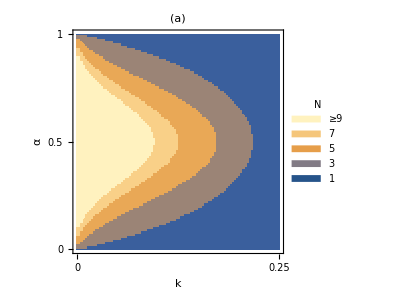

```mathematica
ncontourplotfullextract=ListContourPlot[
Import["data\\fullbatchmachinen-asteps100-ksteps100-maxn9.dat"]⟦All,{2,1,3}⟧,
InterpolationOrder->0,
FrameLabel->{"k","α"},
PlotLabel->"(a)",
RotateLabel->False,
PlotRange->{{0,0.25},{0,1}},
Frame->True,
FrameTicks->{{0,0.25},{0,0.5,1}},
PlotLegends->SwatchLegend[
"M10DefaultDensityGradient",
Range[1,7,2]~Join~{"≥9"},
LegendLayout->(Grid[Reverse[#]]&),
LegendLabel->"N"
],
ImageSize->300
]
```

## (b)

Compile ‘fullbatchmachinework.c’

```mathematica
Run["START /B gcc c\\functions.c c\\fullbatchmachinework.c -o c\\fullbatchmachinework"]
```

0

Create a function that runs ‘fullbatchmachinework.exe’ for a set of inputs and sends the output to an appropriately named .dat file

```mathematica
fullbatchmachinework[asteps_,ksteps_,maxn_]:=Run["START /B c\\fullbatchmachinework "<>ToString[asteps]<>" "<>ToString[ksteps]<>" "<>ToString[maxn]<>" > data\\fullbatchmachinework-asteps"<>ToString[asteps]<>"-ksteps"<>ToString[ksteps]<>"-maxn"<>ToString[maxn]<>".dat"]
```

```mathematica
fullbatchmachinework[20,20,9]
```

0

Create a function that takes in a data file that contains the full batch machine work for various values of k and α and outputs a file containing the ratio of the full batch machine work to the Markov machine work at the same points.

```mathematica
fullbatchmachineratio[fullbatchworkdatafilename_]:=
Export[
StringReplace[fullbatchworkdatafilename,"fullbatchmachinework"->"fullbatchmachineratio"],
{#⟦1⟧,#⟦2⟧,#⟦3⟧/markovwork[#⟦1⟧,#⟦2⟧]}&/@Import[fullbatchworkdatafilename]
]
```

```mathematica
fullbatchmachineratio["data\\fullbatchmachinework-asteps20-ksteps20-maxn9.dat"]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

data\fullbatchmachineratio-asteps20-ksteps20-maxn9.dat

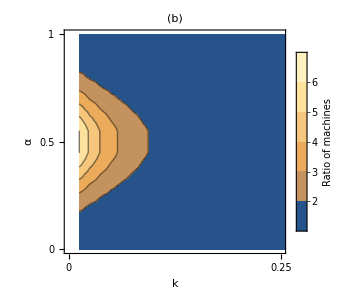

```mathematica
workcontourplotfullextract=ListContourPlot[
Import["data\\fullbatchmachineratio-asteps20-ksteps20-maxn9.dat"]⟦All,{2,1,3}⟧,
FrameLabel->{"k","α"},
PlotLabel->"(b)",
RotateLabel->False,
PlotRange->{{0,0.25},All,All},
FrameTicks->{{0,0.25},{0,0.5,1}},
PlotLegends->BarLegend[
Automatic,
Ticks->Transpose[{#⟦1⟧,#⟦2⟧}&[{{1,2,3,4,5,6},{1,2,3,4,5,6}}]],
LegendLabel->"Ratio of\nmachines"
],
Contours->{2,3,4,5,6},
ImageSize->300
]
```

## (c)

Compile ‘fullbatchefficiency.c’

```mathematica
Run["START /B gcc c\\functions.c c\\fullbatchefficiency.c -o c\\fullbatchefficiency"]
```

0

Create a function that runs ‘fullbatchefficiency.exe’ for a set of inputs and sends the output to an appropriately named .dat file

```mathematica
fullbatchefficiency[asteps_,ksteps_,maxn_,maxk_,entropyn_]:=Run["START /B c\\fullbatchefficiency "<>ToString[asteps]<>" "<>ToString[ksteps]<>" "<>ToString[maxn]<>" "<>ToString[maxk]<>" "<>ToString[entropyn]<>" > data\\fullbatchefficiency-asteps"<>ToString[asteps]<>"-ksteps"<>ToString[ksteps]<>"-maxn"<>ToString[maxn]<>"-maxk"<>ToString[maxk]<>"-entropyn"<>ToString[entropyn]<>".dat"]
```

```mathematica
fullbatchefficiency[5,5,10,1,10]
```

0

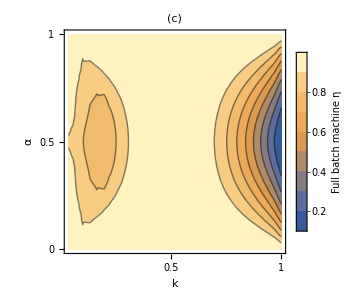

```mathematica
efficiencycontourplotfullextract=ListContourPlot[
Import["data\\fullbatchefficiency-asteps31-ksteps31-maxn9-maxk1-entropyn20.dat"]⟦All,{2,1,3}⟧,
FrameLabel->{"k","α"},
PlotLabel->"(c)",
RotateLabel->False,
FrameTicks->{{0,0.5,1},{0,0.5,1}},
PlotLegends->BarLegend[
Automatic,
Ticks->Transpose[{#⟦1⟧,#⟦2⟧}&[{{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1},{0,"",0.2,"",0.4,"",0.6,"",0.8,"",1}}]],
LegendLabel->"Full batch\nmachine η"
],
Contours->{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},
ImageSize->300
]
```

## Whole figure

```mathematica
complexbatchplot=Grid[{{ncontourplotfullextract,workcontourplotfullextract,efficiencycontourplotfullextract}}]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
Export["complexbatchplot.pdf",complexbatchplot]
```

complexbatchplot.pdf

# FIG 11. Fluctuations

## (a)

This cell calculates the mean infimum of trajectories of the Markov machine by simulation and outputs the data to an appropriately named file.
‘m’ is the number on input molecules in a trajectory.
‘trajectories’ is the number of trajectories in the simulation.
To make the contour plot the mean infimum is calculated for a grid of parameter values.
‘dk’ is the step size in the k parameter.
‘da’ is the step size in the α parameter.

```mathematica
With[{m=100,trajectories=10000,dk=0.02,da=0.02},
Export["data\\makovinfimumcontour-molecules"<>StringReplace[ToString[m]<>"-trajectories"<>ToString[trajectories]<>"-dk"<>ToString[dk]<>"-da"<>ToString[da],"."->"_"]<>".dat",
Flatten[
{#,{#⟦1⟧,1-#⟦2⟧,#⟦3⟧}}&/@Flatten[Table[
If[a==0,Print[k]];
{k,a}~Join~
Mean[Table[
{#⟦-1⟧,Min[#]}&@
((*Make trajectories start at zero*){0}~Join~Accumulate[
(*The two states are symetric so we only need to check if sucessive inputs are the same*)
Log[2]+Log[If[#⟦1⟧==#⟦2⟧,1/2(1+(1-2a)^2(1-2k)),1/2(1-(1-2a)^2(1-2k))]]&/@
(*To calculate the work we need all overlapping pairs of inputs*)
Partition[
(*To get the input I saple 1s with probability α and then XOR them with the hidden state*)
Mod[RandomChoice[{1-a,a}->{0,1},m+1]+
(*This part does the hidden state*)
Mod[Accumulate[{(*I need to start with a uniform hidden state*)RandomInteger[1]}~Join~RandomChoice[{1-k,k}->{0,1},m]],2],2],
2,1]
]),
{trajectories}]],
{k,0,1,dk},{a,0,0.5,da}],
1],
1]
]
]
```

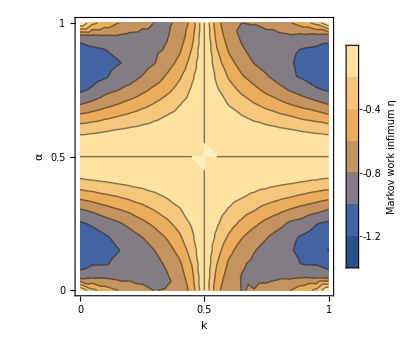

```mathematica
markovfluctuations=ListContourPlot[
Import["data\\makovinfimumcontour-molecules100-trajectories10000-dk0_05-da0_05.dat"]⟦All,{1,2,4}⟧,
PlotRange->{{0,1},{0,1}},
FrameLabel->{"k","α"},
RotateLabel->False,
FrameTicks->({#,None}&/@(Function[list,Transpose[{list,list}]]/@{{0,0.5,1},{0,0.5,1}})),
PlotLegends->BarLegend[
Automatic,
Ticks->Transpose[{#⟦1⟧,#⟦2⟧}&[{{-1.2,-1,-0.8,-0.6,-0.4,-0.2,0},{-1.2,"",-0.8,"",-0.4,"",0}}]],
LegendLabel->"Markov\nwork infimum η"
],
ImageSize->350
]
```

## (b)

Compile ‘batchmeaninfimumcontour.c’

```mathematica
Run["START /B gcc c\\functions.c c\\batchmeaninfimumcontour.c -o c\\batchmeaninfimumcontour"]
```

0

Create a function that runs ‘batchmeaninfimumcontour.exe’ for a set of inputs and sends the output to an appropriately named .dat file

```mathematica
calculatebatchmeaninfimumcontour[asteps_,ksteps_,molecules_,trajectories_,maxk_]:=Run["START /B c\\batchmeaninfimumcontour "<>ToString[asteps]<>" "<>ToString[ksteps]<>" "<>ToString[molecules]<>" "<>ToString[trajectories]<>" "<>ToString[maxk]<>" > data\\batchmeaninfimumcontour-asteps"<>ToString[asteps]<>"-ksteps"<>ToString[ksteps]<>"-molecules"<>ToString[molecules]<>"-trajectories"<>ToString[trajectories]<>"-maxk"<>ToString[maxk]<>".dat"]
```

```mathematica
calculatebatchmeaninfimumcontour[10,10,100,100000,1]
```

0

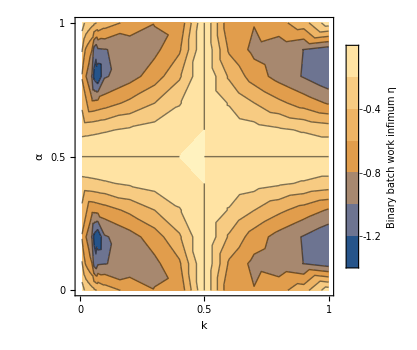

```mathematica
batchfluctuations=ListContourPlot[
Import["data\\batchmeaninfimumcontour-asteps10-ksteps10-molecules100-trajectories100000-maxk0.08.dat"]~Join~Import["data\\batchmeaninfimumcontour-asteps10-ksteps10-molecules100-trajectories100000-maxk1..dat"],
PlotRange->{{0,1},{0,1}},
FrameLabel->{"k","α"},
RotateLabel->False,
FrameTicks->({#,None}&/@(Function[list,Transpose[{list,list}]]/@{{0,0.5,1},{0,0.5,1}})),
PlotLegends->BarLegend[
Automatic,
Ticks->Transpose[{#⟦1⟧,#⟦2⟧}&[{{-1.2,-1,-0.8,-0.6,-0.4,-0.2,0},{-1.2,"",-0.8,"",-0.4,"",0}}]],
LegendLabel->"Binary batch\nwork infimum η"
],
ImageSize->350
]
```

## Whole figure

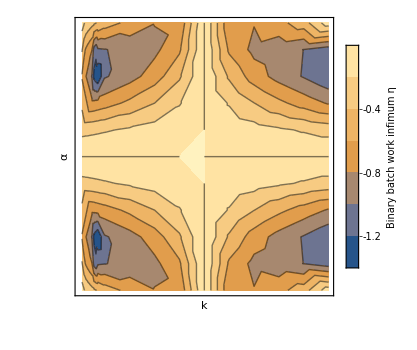
-Graphics-
-Graphics-

```mathematica
fluctuationsplot=Grid[{{markovfluctuations},{batchfluctuations}}]
```

```mathematica
Export["fluctuationsplot.pdf",fluctuationsplot]
```

fluctuationsplot.pdf